```mathematica
n=100;m=50000;
r=Accumulate/@Table[RandomVariate[NormalDistribution[0,Sqrt[1/n]],n],{i,1,m}];
W[t_,k_]:=r[[k,Floor[t n]]]
test=Table[W[0.4,k],{k,1,m}];
Mean[test]
Variance[test]
```

-0.00300702

0.402194

```mathematica
μ=.075;σ=.4;
xx[t_,k_]:=Exp[σ W[t,k]+(μ-σ^2/2)t];
```

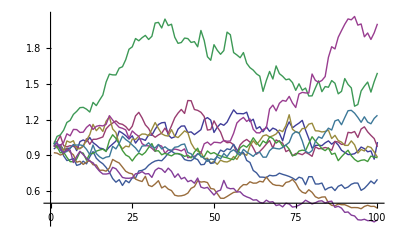

```mathematica
l=3300;ListLinePlot[Table[xx[i/n,l+s],{s,1,10},{i,1,n}]]
```